Kinematics of three-wheeled omnidirectional mobile robot

```mathematica
Clear["Global`*"];
```

### Basic Kinematics

```mathematica
vWheels={vA,vB,vC};
A=({{-Sin[φA], Cos[φA], r}, {-Sin[φB], Cos[φB], r}, {-Sin[φC], Cos[φC], r}});
```

```mathematica
vRobot={u,v,ω};
{vA,vB,vC}=A.vRobot;
%//MatrixForm
```

(r ω+v Cos[φA]-u Sin[φA]
r ω+v Cos[φB]-u Sin[φB]
r ω+v Cos[φC]-u Sin[φC])

```mathematica
({{r ω+v Cos[φA]-u Sin[φA]}, {r ω+v Cos[φB]-u Sin[φB]}, {r ω+v Cos[φC]-u Sin[φC]}})
```

{r ω+v Cos[φA]-u Sin[φA],r ω+v Cos[φB]-u Sin[φB],r ω+v Cos[φC]-u Sin[φC]}

```mathematica
Inverse[A]//MatrixForm;
```

```mathematica
Inverse[A].{VA,VB,VC}/.{v->0,u->0}//MatrixForm//Simplify;
```

### Robot Definition

```mathematica
φA=π/6; φB=φA+(2π)/3;φC=φB+(2π)/3;wheelCircleRadius=0.12;A=({{-Sin[φA], Cos[φA], wheelCircleRadius}, {-Sin[φB], Cos[φB], wheelCircleRadius}, {-Sin[φC], Cos[φC], wheelCircleRadius}});
initialPos={0,0,0};
wheelDiameter=wheelCircleRadius; wheelWidth=wheelCircleRadius/5;wheelRadius = 0.03;
wheelPosA={wheelCircleRadius Cos[φA],wheelCircleRadius Sin[φA],φA+π/2};wheelPosB={wheelCircleRadius Cos[φB],wheelCircleRadius Sin[φB],φB+π/2};wheelPosC={wheelCircleRadius Cos[φC],wheelCircleRadius Sin[φC],φC+π/2};
wheelPosABC={wheelPosA,wheelPosB,wheelPosC};
```

```mathematica
A//MatrixForm;
```

```mathematica
A.{u,v,w}//MatrixForm//N
```

(-0.5 u+0.866025 v+0.12 w
-0.5 u-0.866025 v+0.12 w
u+0.12 w)

```mathematica
AINV=Inverse@A;
%//MatrixForm;
```

```mathematica
AINV.{va,vb,vc}//MatrixForm
```

(-0.333333 va-0.333333 vb+0.666667 vc
0.+0.57735 va-0.57735 vb
2.77778 va+2.77778 vb+2.77778 vc)

#### Some calculations

```mathematica
maxWheelSpeedRPM = 100  (*rpm*)
maxTranslationSpeedSI = AINV.{maxWheelSpeedRPM,-maxWheelSpeedRPM,0}(*m/s*)
maxAngularSpeedSI = AINV.{maxWheelSpeedRPM,maxWheelSpeedRPM,maxWheelSpeedRPM}//Chop (*rad/s*)
```

100

{0.,115.47,0.}

{0,0,833.333}

```mathematica
maxWheelSpeedSI = 100  (2 π)/60 wheelRadius(*m/s*)
maxTranslationSpeedSI = AINV.{maxWheelSpeedSI,-maxWheelSpeedSI,0}(*m/s*)
maxAngularSpeedSI = AINV.{maxWheelSpeedSI,maxWheelSpeedSI,maxWheelSpeedSI}//Chop (*rad/s*)
```

0.314159

{0.,0.36276,0.}

{0,0,2.61799}

```mathematica
vMax = Max[maxTranslationSpeedSI];ωMax = Max[maxAngularSpeedSI];
```

```mathematica
A.{1,0,0}
```

{-0.5,-0.5,1.}

```mathematica
A.{1,1,1}/Max[Abs[A.{1,1,1}]]
```

{0.390061,-1.,0.898858}

```mathematica
RobotCaseGraphics={
Pink,
Disk[{0,0},wheelCircleRadius],
Gray,Triangle[{{-wheelDiameter/2,-wheelDiameter/2},{wheelDiameter/2,-wheelDiameter/2},{0,wheelDiameter/3}}],
Black,
Disk[{0,0},wheelCircleRadius/20],
Gray,
Rotate[Rectangle[{-wheelDiameter/2+wheelPosA[[1]],-wheelWidth/2+wheelPosA[[2]]},{wheelDiameter/2+wheelPosA[[1]],wheelWidth/2+wheelPosA[[2]]}],wheelPosA[[3]]],
Rotate[Rectangle[{-wheelDiameter/2+wheelPosB[[1]],-wheelWidth/2+wheelPosB[[2]]},{wheelDiameter/2+wheelPosB[[1]],wheelWidth/2+wheelPosB[[2]]}],wheelPosB[[3]]],
Rotate[Rectangle[{-wheelDiameter/2+wheelPosC[[1]],-wheelWidth/2+wheelPosC[[2]]},{wheelDiameter/2+wheelPosC[[1]],wheelWidth/2+wheelPosC[[2]]}],wheelPosC[[3]]]
};
```

```mathematica
TranslateAndRotate[g_,x_,y_,α_]:=Module[{},Rotate[Translate[g,{x,y}],α,{x,y}]]
```

```mathematica
DrawRobot[{x_,y_,α_}]:={EdgeForm[Black],Rotate[Translate[RobotCaseGraphics,{x,y}],α,{x,y}]}
```

```mathematica
Graphics[DrawRobot[{0,0,0}],Axes->True]
```

-Graphics-

```mathematica
WheelVectors[{vA_,vB_,vC_,λ_}]:={
velocities ={vA,vB,vC};
locations ={wheelPosABC⟦1⟧⟦1;;2⟧,wheelPosABC⟦2⟧⟦1;;2⟧,wheelPosABC⟦3⟧⟦1;;2⟧};
directions = {{Cos[wheelPosABC⟦1⟧⟦3⟧],Sin[wheelPosABC⟦1⟧⟦3⟧]},{Cos[wheelPosABC⟦2⟧⟦3⟧],Sin[wheelPosABC⟦2⟧⟦3⟧]},{Cos[wheelPosABC⟦3⟧⟦3⟧],Sin[wheelPosABC⟦3⟧⟦3⟧]}};
texts={"vA","vB","vC"};

index=1;
Red,Arrow[{locations[[index]],locations[[index]]+λ velocities[[index]] directions[[index]]}],
Text[Style[texts[[index]],Black],(locations[[index]]+λ velocities[[index]] directions[[index]]+ {wheelCircleRadius/3,wheelCircleRadius/5})];

index=2;
Green,Arrow[{locations[[index]],locations[[index]]+λ velocities[[index]] directions[[index]]}],
Text[Style[texts[[index]],Black],(locations[[index]]+λ velocities[[index]] directions[[index]]+ {wheelCircleRadius/3,wheelCircleRadius/5})];

index=3;
Blue,Arrow[{locations[[index]],locations[[index]]+λ velocities[[index]] directions[[index]]}],
Text[Style[texts[[index]],Black],(locations[[index]]+λ velocities[[index]] directions[[index]]+ {wheelCircleRadius/3,wheelCircleRadius/5})];

(*Black,Arrow[{{0,0},{0,wheelCircleRadius/3}}],Text[Style["",Black],({0,wheelCircleRadius/3}) 1.5];*)
}
```

```mathematica
DrawWheelVectors[{x_,y_,α_,vA_,vB_,vC_,λ_}]:={EdgeForm[Black],TranslateAndRotate[WheelVectors[{vA,vB,vC,λ}],x,y,α]}
```

```mathematica
DrawWheelVectors[{0,0,π/12,2,1,1,1}]//Graphics;
```

```mathematica
DrawVelocityVector[{x_,y_,α_,vx_,vy_,λ_}]:={EdgeForm[Black],TranslateAndRotate[{
Black,Arrow[{{0,0},{0,0}+λ{vx,vy}}],
Text[Style["v",Black],( {wheelCircleRadius/3,wheelCircleRadius/5})];
},x,y,α]}
```

```mathematica
DrawVelocityVector[{0,0,π/12,0,1,1}]//Graphics;
```

### Kinematic Simulation

```mathematica
CalculateOneStep[{x_,y_,α_,v_,γ_,ω_,dt_}]:=Module[{vx,vy,vRobot,vWheels,vA,vB,vC,newpos,newx,newy,newr,newv,newγ,newvx,newvy,newω,newvWheels,newvA,newvB,newvC,λ},
vx=-v Sin[γ];
vy=v Cos[γ];
vRobot={vx,vy}~Join~{ω};
vWheels=A.vRobot;
vA=vWheels⟦1⟧;vB=vWheels⟦2⟧;vC=vWheels⟦3⟧;
λ1=6wheelCircleRadius/v ;λ2=6wheelCircleRadius/v;
show1 = Graphics[DrawRobot[{x,y,α}]];
show2 = Graphics[DrawWheelVectors[{x,y,α,vA,vB,vC,λ1}]]; 
show3 = Graphics[DrawVelocityVector[{x,y,α,vx,vy,λ2}]]; 
newpos= {x,y}+RotationMatrix[α,{0,0,1}][[1;;2,1;;2]].{vx,vy}*dt;newx=N@newpos[[1]];newy=N@newpos[[2]];
newr=α+ω dt;
newv = v;
newγ = γ-ω dt;
newvx=-newv Sin[newγ];
newvy=newv Cos[newγ];
newω = ω;
newvWheels=A.({newvx,newvy}~Join~{newω});
newvA=vWheels⟦1⟧;newvB=vWheels⟦2⟧;newvC=vWheels⟦3⟧;
show4 = Graphics[DrawRobot[{newx,newy,newr}]];
show5 = Graphics[DrawWheelVectors[{newx,newy,newr,newvA,newvB,newvC,λ1}]]; 
show6= Graphics[DrawVelocityVector[{newx,newy,newr,newvx,newvy,λ2}]]; 
show7 = 
Graphics[{
PointSize[Large],Point[newpos],
Text[
"{x,y}: "<>ToString[N@newpos]<>"\n α: "<>ToString[180/π N@newr]<>"°\n",
{-1,-1}]
}];
Show[show1,show2,show3,show4,show5,show6,show7,PlotRange->{{-2,2},{-2,2}},Axes->True]
]
```

```mathematica
Manipulate[CalculateOneStep[{x,y,α,v,γ,ω,dt}],
{{x,0.0},-2,2},
{{y,0.0},-2,2},
{{α,0},-2π,2 π},
{{v,vMax/2},-vMax,vMax},
{{γ,0},-2π,2π},
{{ω,0},-ωMax,ωMax},
{{dt,1},0,10,1},
SaveDefinitions->True]
```

```mathematica
CalculateNewState[{x_,y_,α_,v_,γ_,ω_,vWheels_,pathVectorX_,pathVectorY_}]:=Module[{vx,vy,vRobot,vA,vB,vC,newpos,newx,newy,newr,newv,newγ,newvx,newvy,newω,newvWheels,newvA,newvB,newvC,newpathVectorX,newpathVectorY},
vx=-v Sin[γ];
vy=v Cos[γ];
newpos= {x,y}+RotationMatrix[α,{0,0,1}][[1;;2,1;;2]].{vx,vy}*dt;
newx=N@newpos[[1]];
newy=N@newpos[[2]];
newr=α+ω dt;
newv = v;
newγ = γ-ω dt+δγ dt;
newvx=-newv Sin[newγ];
newvy=newv Cos[newγ];
newω = ω+RandomReal[{-1,1}]×0 ;
newvWheels=A.({newvx,newvy}~Join~{newω});
newvA=newvWheels⟦1⟧;
newvB=newvWheels⟦2⟧;
newvC=newvWheels⟦3⟧;
newpathVectorX=Append[pathVectorX,newx];
newpathVectorY=Append[pathVectorY,newy];
{newx,newy,newr,newv,newγ,newω,newvWheels,newpathVectorX,newpathVectorY}
]
```

```mathematica
DrawPath[{newpathVectorX_,newpathVectorY_}]:={Opacity[0.5],Black,PointSize[Tiny],Point[Transpose[{newpathVectorX,newpathVectorY}]]}
```

```mathematica
steps=100; dt=.1;
x0=0.0;y0=0.5; α0=π/2;pathVectorX0={x0};pathVectorY0={y0};
v0 = .2; γ0=0;ω0=N@((-2 π)/(dt steps)) ;δγ=(2 π)/(dt steps);
λ1=6wheelCircleRadius/v0;λ2=6wheelCircleRadius/v0;
vWheels0=A.{-v0 Sin[γ0],v0 Cos[γ0],ω0};
Motion=NestList[CalculateNewState,{x0,y0,α0,v0,γ0,ω0,vWheels0,pathVectorX0,pathVectorY0},steps+1];
%//MatrixForm;
```

```mathematica
ShowResults[{newx_,newy_,newr_,newv_,newγ_,newω_,newvWheels_,newpathVectorX_,newpathVectorY_}]:=
Graphics[{
DrawPath[{newpathVectorX,newpathVectorY}],
DrawRobot[{newx,newy,newr}],
DrawWheelVectors[{newx,newy,newr,newvWheels⟦1⟧,newvWheels⟦2⟧,newvWheels⟦3⟧,λ1}],
DrawVelocityVector[{newx,newy,newr,-Sin[newγ] newv,Cos[newγ] newv,λ2}]},
PlotRange->{{-1,1},{-1,1}},Frame->True
]
```

```mathematica
Manipulate[Evaluate[ShowResults[Motion[[i]]]],
{i,1,steps+1,1},SaveDefinitions->True]
```

Part::pkspec1: The expression i cannot be used as a part specification.

```mathematica
Anim=Table[ShowResults[Motion[[i]]],{i,1,steps+1}];
SetDirectory[NotebookDirectory[]];
(*Export["3DOF_moving.gif",Anim]*)
```

```mathematica
DSolve[θ x''[t]+b x'[t]==M,x[t],t]
```

{{x[t]→(M t)/b-(ⅇ^(-(b t)/θ) θ C[1])/b+C[2]}}

```mathematica
eq1=θ x''[t]+b x'[t]==M;eq2=x[0]==0;eq3=x'[0]==0;
```

```mathematica
solution=DSolve[{eq1/.{θ->0.00011,b->0.001,M->0.11},eq2,eq3},x[t],t][[1]]
```

{x[t]→110. ⅇ^(-9.09091 t) (0.11-0.11 ⅇ^(9.09091 t)+1. ⅇ^(9.09091 t) t)}

```mathematica
velocity = D[D[x[t]/.solution,t],t];
```

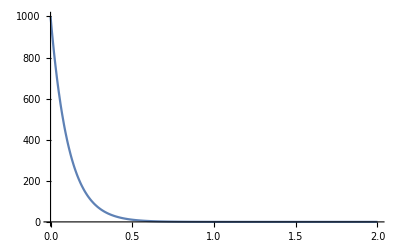

```mathematica
Plot[velocity,{t,0,2},PlotRange->All]
```

```mathematica
omega[t] = 110 (2 π)/60(1-E^(-t/0.11))
```

11/3 (1-ⅇ^(-9.09091 t)) π

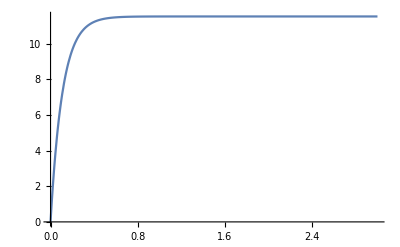

```mathematica
Plot[omega[t],{t,0,3},PlotRange->All]
```

```mathematica
epsilon[t]=D[omega[t],t]
```

104.72 ⅇ^(-9.09091 t)

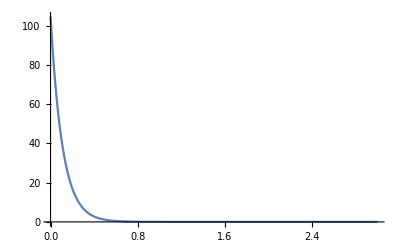

```mathematica
Plot[epsilon[t],{t,0,3},PlotRange->All]
```

```mathematica
θ->0.00011,b->0.001,M->0.11
```

```mathematica
M[t] = 0.001 omega[t] + 0.00011 epsilon[t]
```

0.0115192 ⅇ^(-9.09091 t)+0.0115192 (1-ⅇ^(-9.09091 t))

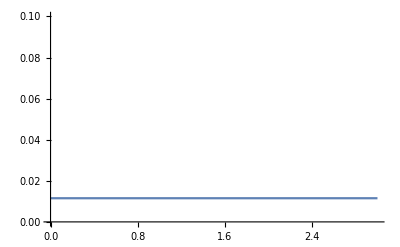

```mathematica
Plot[M[t],{t,0,3},PlotRange->{0,0.1}]
```